```mathematica
Clear["Global`*"]
```

```mathematica
b=8
```

8

```mathematica
V[u_]:=u^2-2 u^3
```

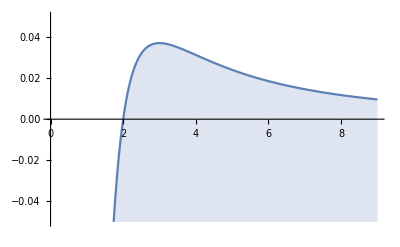

```mathematica
Veff=Plot[V[1/r],{r,0,9},Filling->Bottom,AxesOrigin->{0,0},PlotRange->0.05]
```

```mathematica
dV:=D[V[u],u]
```

```mathematica
max=1/3
```

1/3

```mathematica
Vmax=V[max]
```

1/27

```mathematica
sce:=Plot[1/b^2,{r,0,9}]
```

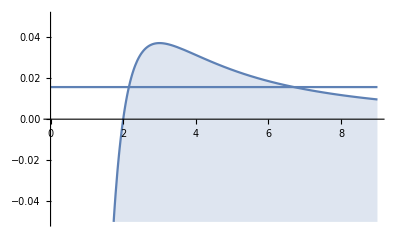

```mathematica
Show[Veff,sce]
```

```mathematica
soln=NSolve[V[tp]==1/b^2,tp]
```

{{tp→-0.112901},{tp→0.149242},{tp→0.463659}}

```mathematica
tp1=tp/.soln[[1]]
tp2=tp/.soln[[2]]
tp3=tp/.soln[[3]]
```

-0.112901

0.149242

0.463659

```mathematica
rst=5
```

5

```mathematica
ust=1/rst
```

1/5

```mathematica
eps=10^-15
```

1/1000000000000000

```mathematica
orbittype:=If[1/b^2==Vmax,"circle",If[1/b^2<Vmax,"scatter","plunge"]]
```

```mathematica
orbittype
```

scatter

```mathematica
norbit=If[orbittype=="plunge",0.5,If[orbittype=="circle",2π,1]]
```

1

```mathematica
u1:=If[orbittype=="circle",tp2(1+eps),ust]
u2:=If[orbittype=="plunge",0.5(1-eps),tp2(1-eps)]
```

```mathematica
norbit
```

1

```mathematica
u1
u2
```

1/5

0.149242

```mathematica
theta[u_,b_,u1_]:=NIntegrate[1/(√(1/b^2-V[w])),{w,u1,u}]
```

```mathematica
delphi=If[orbittype=="circle",0,theta[u2,b,u1]]
```

-1.95457×10^-7+1.10732 ⅈ

```mathematica
n[z_]:=IntegerPart[z]
zf[z_]:=FractionalPart[z]
```

```mathematica
ua[z_]:=u1(1-2zf[z])+u2  2  zf[z]
```

```mathematica
ub[z_]:=u1(2 zf[z]-1)+2 u2 (1-zf[z])
```

```mathematica
u[z_]:=If[zf[z]<.5,ua[z],ub[z]]
```

```mathematica
phia[z_]:=2(n [z])delphi+theta[u[z],b,u1]
```

```mathematica
phib[z_]:=2(n [z] +1)delphi-theta[u[z],b,u1]
```

```mathematica
accphi[z_]:=If[orbittype=="circle",z, If[zf[z]<.5,phia[z],phib[z]]]
```

```mathematica
x[z_]:=Cos[accphi[z]]/u[z]
```

```mathematica
y[z_]:=Sin[accphi[z]]/u[z]
```

```mathematica
graph = ParametricPlot[{x[t],y[t]},{t,0,norbit},PlotRange->5]
```

-Graphics-

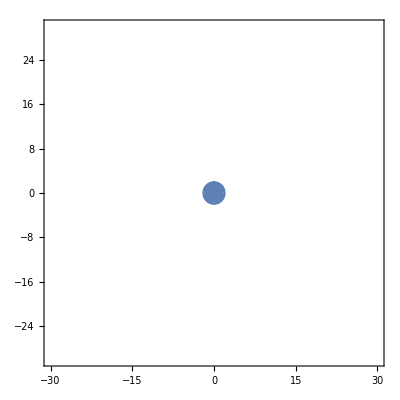

```mathematica
eh=ParametricPlot[{r Sin[k],r Cos[k]},{k,0,2π},{r,0,2},PlotRange->30,Mesh->False]
```

```mathematica
Show[eh,graph]
```

-Graphics-

```mathematica
delphi/Degree
```

-0.0000111989+63.445 ⅈ